```mathematica
Grad[x^2+y^2, {x,y}]
```

{2 x,2 y}

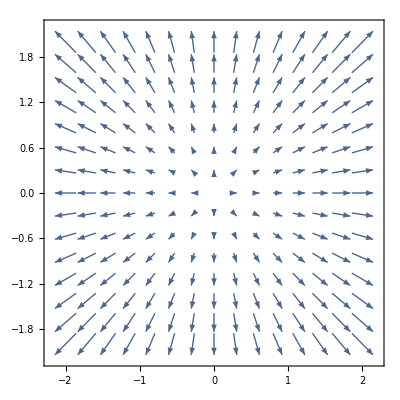

```mathematica
VectorPlot[Evaluate[Grad[x^2+y^2, {x,y}]], {x, -2, 2}, {y, -2, 2}]
```

```mathematica
f[x_, y_]:=x^2-y^2
```

```mathematica
Plot3D[{f[x,y],0},{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Solve[(x-2)(x+2)==0 && x> 0, x]
```

{{x→2}}

```mathematica
(*Часть 0*)
```

```mathematica
TangentPlane[f_,x0_,y0_]:=(
grad = Grad[f, {x,y}];
Return[(grad/.x->x0/. y->y0).{x-x0,y-y0} + (f/.x->x0/.y->y0)]
)
```

```mathematica
TangentPlane[(x-2)^2+4*y^2, 2,0]
```

0

```mathematica
Plot3D[{(x-2)^2+4*y^2, 0}, {x,1,3}, {y, -2, 2}]
```

-Graphics3D-

```mathematica
z = TangentPlane[(x-2)^2+4*y^2, 2,1]
```

4+8 (-1+y)

```mathematica
Plot3D[{(x-2)^2+4*y^2, z}, {x,1,3}, {y, -2, 2}]
```

-Graphics3D-

```mathematica
(*функция касательной плоскости к критической точке функции двух переменных выглядит как z=const, так как градиент равен нулю, то же самое с функцией трех переменных.*)
```

```mathematica
(*Локальные экстремумы функций двух переменных*)
```

```mathematica
(*1*)
```

```mathematica
f1[x_,y_]:=x*y;
```

```mathematica
Plot3D[f1[x,y],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
grad1 = Grad[f1[x,y], {x,y}];
```

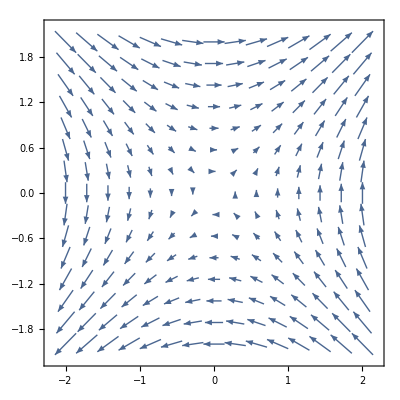

```mathematica
VectorPlot[Evaluate[grad1], {x, -2, 2}, {y, -2, 2}]
```

```mathematica
Solve[grad1==0, {x, y}]
```

{{x→0,y→0}}

```mathematica
t1 = TangentPlane[f1[x,y], 0, 0]
```

0

```mathematica
Plot3D[{f1[x,y], t1}, {x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
(*точка (0,0) выглядит как седловая*)
```

```mathematica
MatrixForm[Grad[grad1,{x,y}]]
```

(0 | 1
1 | 0)

```mathematica
(*первый элемент матрицы = 0, следовательно форма не определена, значит точка (0,0) седловая*)
```

```mathematica
(*2*)
```

```mathematica
f2[x_,y_]:=x*ⅇ^(-x^2-y^2);
```

```mathematica
Plot3D[f2[x,y],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
grad2 = Grad[f2[x,y], {x,y}];
```

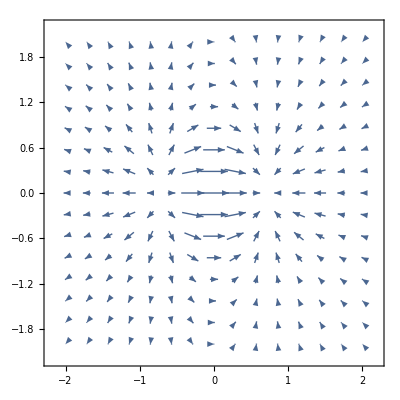

```mathematica
VectorPlot[Evaluate[grad2], {x, -2, 2}, {y, -2, 2}]
```

```mathematica
Solve[grad2==0, {x, y}]
```

{{x→-1/(√2),y→0},{x→1/(√2),y→0}}

```mathematica
t21 = TangentPlane[f2[x,y], -1/(√2), 0]
```

-1/(√(2 ⅇ))

```mathematica
Plot3D[{f2[x,y], t21}, {x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
(*точка (-1/(√2), 0) выглядит как точка минимума*)
```

```mathematica
t22 =  TangentPlane[f2[x,y], 1/(√2), 0]
```

1/(√(2 ⅇ))

```mathematica
Plot3D[{f2[x,y], t22}, {x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
(*точка (1/(√2), 0) выглядит как точка максимума*)
```

```mathematica
m2 = MatrixForm[Grad[grad2,{x,y}]]/.{x->-1/(√2),y->0}
```

(2 √(2/ⅇ) | 0
0 | √(2/ⅇ))

```mathematica
m21=Grad[grad2,{x,y}]/.{x->-1/(√2),y->0};
```

```mathematica
Det[m21]
```

4/ⅇ

```mathematica
(*первый элемент положителен, и детерминант положителен, форма положительно определена, значит точка (-1/(√2),0) - минимум*)
```

```mathematica
m22=Grad[grad2,{x,y}]/.{x->1/(√2),y->0}
```

{{-2 √(2/ⅇ),0},{0,-√(2/ⅇ)}}

```mathematica
Det[m22]
```

4/ⅇ

```mathematica
(*первый элемент отрицателен, и детерминант положителен, форма отрицательно определена, значит точка (1/(√2),0) - максимум*)
```

```mathematica
(* (-1/(√2),0) - минимум функции, (1/(√2),0) - точка максимума.*)
```

```mathematica
(*3*)
```

```mathematica
f3[x_,y_]:=x*y/(x^2+y^2+1);
```

```mathematica
Plot3D[f3[x,y],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
grad3 = Grad[f3[x,y], {x,y}];
```

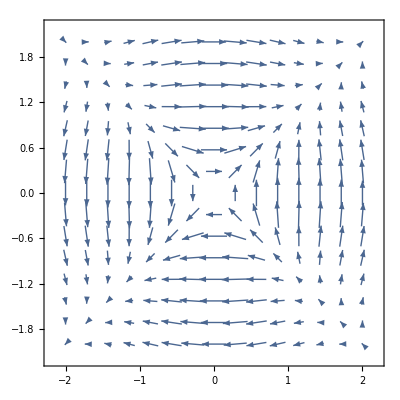

```mathematica
VectorPlot[Evaluate[grad3], {x, -2, 2}, {y, -2, 2}]
```

```mathematica
Solve[grad3==0, {x, y}]
```

{{x→0,y→0}}

```mathematica
t3= TangentPlane[f3[x,y], 0, 0]
```

0

```mathematica
Plot3D[{f3[x,y], t3}, {x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
(*(0,0) выглядит как седловая точка*)
```

```mathematica
m3 = MatrixForm[Grad[grad3,{x,y}]]/.{x->0,y->0}
```

(0 | 1
1 | 0)

```mathematica
(*первый элемент в матрице = 0, значит(0,0) - седловая точка.*)
```

```mathematica
(*4*)
```

```mathematica
f4[x_,y_]:=Cos[x]+Cos[y];
```

```mathematica
Plot3D[f4[x,y],{x,-π/2,3π/2},{y,-3π/2,2π}]
```

-Graphics3D-

```mathematica
grad4 = Grad[f4[x,y], {x,y}];
```

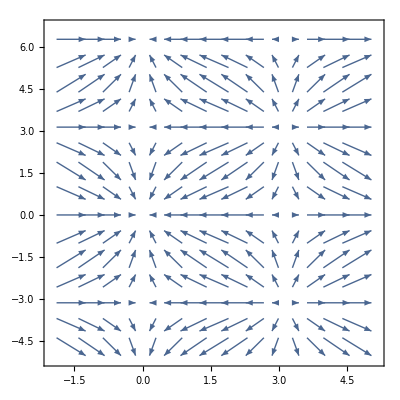

```mathematica
VectorPlot[Evaluate[grad4], {x,-π/2,3π/2},{y,-3π/2,2π}]
```

```mathematica
Solve[grad4==0 && x≥-π/2 &&x≤3π/2 && y≥-3π/2 && y≤π/2,{x, y} ]
```

{{x→0,y→0},{x→π,y→0},{x→0,y→-π},{x→π,y→-π}}

```mathematica
t41= TangentPlane[f4[x,y], 0, 0]
```

2

```mathematica
Plot3D[{f4[x,y], t41}, {x,-π/2,3π/2},{y,-3π/2,2π}]
```

-Graphics3D-

```mathematica
(*(0,0) выглядит как точка максимума*)
```

```mathematica
t42= TangentPlane[f4[x,y], -π, 0]
```

0

```mathematica
Plot3D[{f4[x,y], t42}, {x,-π/2,3π/2},{y,-3π/2,2π}]
```

-Graphics3D-

```mathematica
(*(-π, 0) выглядит как седло*)
```

```mathematica
t43= TangentPlane[f4[x,y], 0, -π]
```

0

```mathematica
Plot3D[{f4[x,y], t43}, {x,-π/2,3π/2},{y,-3π/2,2π}]
```

-Graphics3D-

```mathematica
(*(0, -π) выглядит как седло*)
```

```mathematica
t44=  TangentPlane[f4[x,y], π, -π]
```

-2

```mathematica
Plot3D[{f4[x,y], t44}, {x,-π/2,3π/2},{y,-3π/2,2π}]
```

-Graphics3D-

```mathematica
(*(π, -π) выглядит как минимум*)
```

```mathematica
m41 = Grad[grad4,{x,y}]/.{x->0,y->0}
```

{{-1,0},{0,-1}}

```mathematica
Det[m41]
```

1

```mathematica
(*в точке (0,0) первый элемент отрицательный, определитель положительный, форма отрицательно определена, значит (0,0) - точка максимума*)
```

```mathematica
m42= Grad[grad4,{x,y}]/.{x->π,y->0}
```

{{1,0},{0,-1}}

```mathematica
Det[m42]
```

-1

```mathematica
(*в точке (π,0) первый элемент положительный, определитель отрицательный, форма не определена, значит (π,0) - седло*)
```

```mathematica
m43= Grad[grad4,{x,y}]/.{x->0,y->-π}
```

{{-1,0},{0,1}}

```mathematica
Det[m43]
```

-1

```mathematica
(*в точке (0,-π) первый элемент отрицательный, определитель отрицательный, форма не определена, значит (0,-π) - седло*)
```

```mathematica
m44 = Grad[grad4,{x,y}]/.{x->π,y->-π}
```

{{1,0},{0,1}}

```mathematica
Det[m44]
```

1

```mathematica
(*в точке (π,π) первый элемент положительный, определитель положительный, форма положительно определена, значит (π,π) - точка минимума*)
```

```mathematica
(*(0,0) - максимум,(π,0) - седло,(0,-π) - седло,(π,-π)-минимум*)
```

```mathematica
(*5*)
```

```mathematica
f5[x_,y_]:=Sin[π*x*Sin[x]+y];
```

```mathematica
Plot3D[f5[x,y],{x,-π,π},{y,-2π,2π}]
```

-Graphics3D-

```mathematica
grad5= Grad[f5[x,y], {x,y}];
```

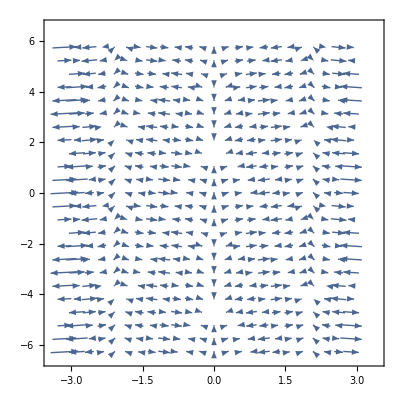

```mathematica
VectorPlot[Evaluate[grad5], {x,-π,π},{y,-2π,2π}, VectorPoints->Fine]
```

```mathematica
sol =Solve[grad5==0 && -Pi<x<Pi && -2Pi <y<2Pi,{x, y} ]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{Cos[y+π x Sin[x]] (π x Cos[x]+π Sin[x]),Cos[y+π x Sin[x]]}==0&&-π<x<π&&-2 π<y<2 π,{x,y}]

```mathematica
FindRoot[grad5==0, {{x, 0}, {y, 0}}]
```

{x→0.,y→0.}

```mathematica
m5  = TangentPlane[f5[x,y], 0, 0]
```

y

```mathematica
m = Grad[grad5,{x,y}]
```

{{Cos[y+π x Sin[x]] (2 π Cos[x]-π x Sin[x])-(π x Cos[x]+π Sin[x])^2 Sin[y+π x Sin[x]],-(π x Cos[x]+π Sin[x]) Sin[y+π x Sin[x]]},{-(π x Cos[x]+π Sin[x]) Sin[y+π x Sin[x]],-Sin[y+π x Sin[x]]}}

```mathematica
Plot3D[{f5[x,y], t5}, {x,-π,π},{y,-2π,2π}]
```

-Graphics3D-

```mathematica
(*получилось нечто странное*)
```

```mathematica
m5=Grad[grad5,{x,y}]/.{x->0,y->0}
```

{{2 π,0},{0,0}}

```mathematica
Det[m5]
```

0

```mathematica
(*определитель матрицы равен нулю, корни не ищутся с помощью Solve, кажется это очень нехорошая функция*)
```

```mathematica
(*6*)
```

```mathematica
f6[x_,y_]:=(ⅇ^-(x-1)^2 + ⅇ^-(x+1)^2)*ⅇ^(-y^2);
```

```mathematica
Plot3D[f6[x,y],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
grad6 = Grad[f6[x,y], {x,y}];
```

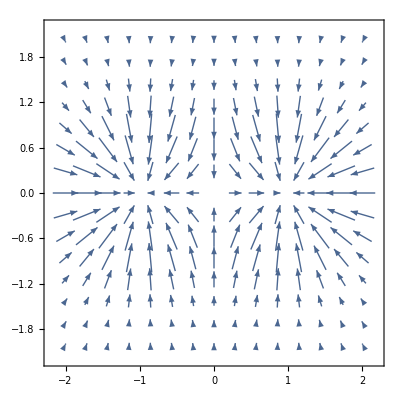

```mathematica
VectorPlot[Evaluate[grad6], {x, -2, 2}, {y, -2, 2}]
```

```mathematica
FindRoot[grad6==0,{{x,0},{y,0}}]
```

{x→0.,y→0.}

```mathematica
t61= TangentPlane[f6[x,y], 0., 0.]
```

0.735759

```mathematica
Plot3D[{f6[x,y], t61}, {x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
(*(0,0) выглядит как седло*)
```

```mathematica
FindRoot[grad6==0,{{x,1},{y,0}}]
```

{x→0.957504,y→0.}

```mathematica
t62= TangentPlane[f6[x,y], 0.9575040240772716, 0]
```

1.01987-4.91274×10^-15 (-0.957504+x)

```mathematica
Plot3D[{f6[x,y], t62}, {x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
(*(0.9575040240772716, 0) выглядит как максимум*)
```

```mathematica
FindRoot[grad6==0,{{x,-1},{y,0}}]
```

{x→-0.957504,y→0.}

```mathematica
t63= TangentPlane[f6[x,y], -0.9575040240772716, 0]
```

1.01987+4.91274×10^-15 (0.957504+x)

```mathematica
Plot3D[{f6[x,y], t63}, {x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
(*(-0.9575040240772716, 0) выглядит как максимум*)
```

```mathematica
m61=Grad[grad6,{x,y}]/.{x->0.,y->0.}
```

{{1.47152,0.},{0.,-1.47152}}

```mathematica
Det[m61]
```

-16/ⅇ^2

```mathematica
(*первый элемент положителен и определитель отрицателен, значит форма не определена и (0,0) - седловая точка*)
```

```mathematica
m62 = Grad[grad6,{x,y}]/.{x->0.9575040240772716,y->0.}
```

{{-1.70038,0.},{0.,-2.03973}}

```mathematica
Det[m62]
```

3.46831

```mathematica
(*первый элемент отрицателен и определитель положителен, значит форма определена отрицательно и (0.9575040240772716,0) - точка максимума*)
```

```mathematica
m63 = Grad[grad6,{x,y}]/.{x->-0.9575040240772716,y->0.}
```

{{-1.70038,0.},{0.,-2.03973}}

```mathematica
Det[m63]
```

3.46831

```mathematica
(*первый элемент отрицателен и определитель положителен, значит форма определена отрицательно и (-0.9575040240772716,0) - точка максимума*)
```

```mathematica
(*(0,0) - седло, (0.9575040240772716,0) - максимум, (-0.9575040240772716,0) - максимум*)
```